```mathematica
ClearAll["Global`*"]
```

## Plot n^th Root of Unity

```mathematica
z[k_, n_] := ⅇ^((k π ⅈ)/n)
```

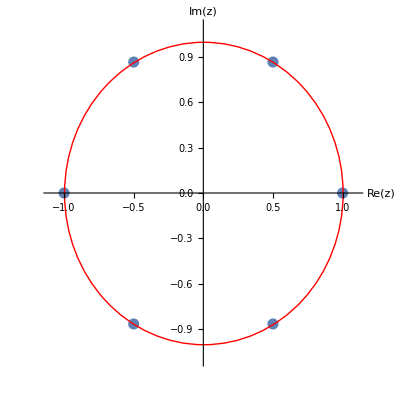

ROOTS:

{1,ⅇ^((ⅈ π)/3),ⅇ^((2 ⅈ π)/3),-1,ⅇ^(-(2 ⅈ π)/3),ⅇ^(-(ⅈ π)/3)}

```mathematica
n:=3
segment:=5
rootplot :=
ListPlot[
Table[{Re[z[k,n]], Im[z[k,n]]}, {k, 0, segment}],
PlotRange-> {{-1.1, 1.1},{-1.1, 1.1}}, 
AxesLabel-> {"Re(z)", "Im(z)"}, 
AspectRatio-> 1, PlotStyle-> PointSize[0.02]
]

Show[rootplot, Graphics[{Red, Circle[{0,0}, 1]}]]

Print[Style["ROOTS:", Red, Bold]]
Table[z[k,n], {k, 0, segment}]
```